SENIOR YEAR SEMESTER 1 NOTES - BC CALCULUS

```mathematica
Now
```

Sat 18 Sep 2021 13:00:23GMT-4.

```mathematica
ArcSin[(-1+Sqrt[33])/8.]
```

0.634867

```mathematica
ourList = 
Flatten @ Values[
NSolve[D[Sin[2x]-Cos[x],x]==0&&-6Pi≤x≤ 6Pi,
x
]
]
```

{-17.8466,-16.7109,-15.0731,-13.2012,-11.5634,-10.4277,-8.78991,-6.91805,-5.28022,-4.14456,-2.50673,-0.634867,1.00297,2.13863,3.77646,5.64832,7.28615,8.42181,10.0596,11.9315,13.5693,14.705,16.3428,18.2147}

```mathematica
Sin[2 5.648318436046016]-Cos[5.64832]
```

-1.76017

```mathematica
Sin[2 3.776459524723364] - Cos[3.7764595247233]
```

1.76017

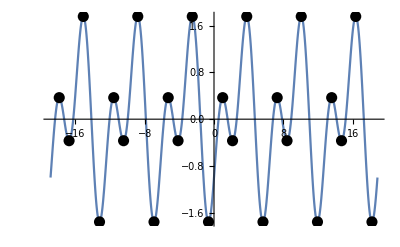

```mathematica
Plot[
Sin[2x]-Cos[x],
{x,-6Pi,6Pi},
Epilog->{
PointSize @ 0.02,
Table[
Point[
{ourList[[n]],Sin[2x]-Cos[x]/.x->ourList[[n]]}
],
{n,1,Length[ourList]}
]
}
]
```

```mathematica
Now
```

Mon 4 Oct 2021 13:52:39GMT-4.

```mathematica
D[x^5,{x,3}]
```

60 x^2

Gives the third derivative of x^5

```mathematica
TableForm@Table[
{
n, 
D[E^x Log[x],{x,n}]/.x->1
},
{n,1,10,1}
]
```

1 | ⅇ
2 | ⅇ
3 | 2 ⅇ
4 | 0
5 | 9 ⅇ
6 | -35 ⅇ
7 | 230 ⅇ
8 | -1624 ⅇ
9 | 13209 ⅇ
10 | -120287 ⅇ

```mathematica
others = Plot[
{x^3,x^4},
{x,-3,3},
PlotStyle->{Black,Dashed}
];
```

```mathematica
dotted = Plot[
x^2,
{x,-3,3},
PlotStyle->{White, Thin},
Mesh->75,
MeshStyle->{Black, PointSize@0.0075},
MeshFunctions->{"ArcLength"}
];
```

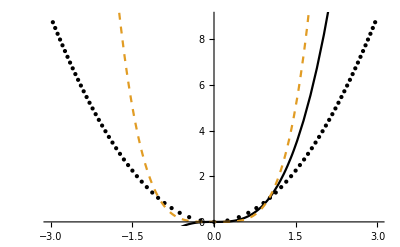

```mathematica
Show[dotted,others]
```

```mathematica
Now
```

Tue 5 Oct 2021 14:43:46GMT-4.

```mathematica
Flatten@Values@Solve[Cos[t]-Sin[t]^2+Cos[t]^2==0&&0≤ t≤ 2Pi,t]
```

{π/3,π,π,(5 π)/3}

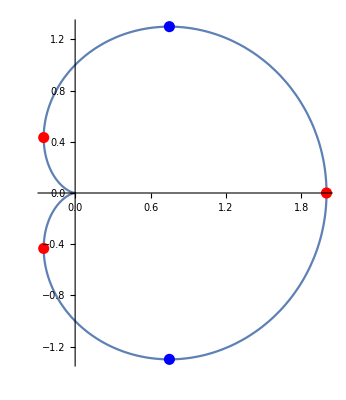

```mathematica
PolarPlot[
1+Cos[t],
{t,0,2Pi},
Epilog->{
Red,PointSize@0.02,
Point[{(1+Cos[#])Cos[#],(1+Cos[#])Sin[#]}]&/@{2Pi/3,4Pi/3,0},
Blue,
Point[{(1+Cos[#])Cos[#],(1+Cos[#])Sin[#]}]&/@{Pi/3,5Pi/3}
(*blue points are when slope = 0, red when slope is infinite (don't include the cusp point)*)
}
]
```

```mathematica
Now
```

Thu 7 Oct 2021 08:48:46GMT-4.

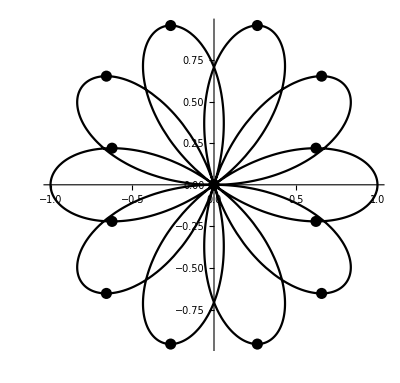

```mathematica
With[
{list = 
Flatten @ Values[
NSolve[D[Sin[x] Cos[5x/2],x]==0&&0≤x≤ 4Pi,
x
]
]
},
PolarPlot[
Cos[5t/2],
{t,0,4Pi},
PlotStyle->Black,
Epilog->{
PointSize@0.02,
Table[
Point[
{Cos[list[[n]]]Cos[5( list[[n]])/2],Sin[list[[n]]]Cos[5 (list[[n]])/2]}
],
{n,1,Length[ourList]}
]
}
]
]
```

```mathematica
Now
```

Fri 8 Oct 2021 09:44:44GMT-4.

```mathematica
Manipulate[
Plot[
{x^4-4x^2,12x^2-8},
{x,-2,2},
PlotStyle->{{Blue,Thick},{Red,Thin}},
PlotRange->{{-2.2,2.2},{-4.2,5}},
Epilog->{
InfiniteLine[{a,x^4-4x^2/.x->a},
{1,4x^3-8x/.x->a}],
PointSize@0.02,
Point[{a,x^4-4x^2/.x->a}]
}
],
{{a,Sqrt[2/3]},-2.2,2.2}
]
```

```mathematica
Now
```

Fri 15 Oct 2021 14:02:29GMT-4.

```mathematica
TableForm[
Table[
{
n,
D[E^x Sin[x],{x,n}],
D[E^x Sin[x],{x,n}]/.x->0
},
{n,0,15}
]
]
```

0 | ⅇ^x Sin[x] | 0
1 | ⅇ^x Cos[x]+ⅇ^x Sin[x] | 1
2 | 2 ⅇ^x Cos[x] | 2
3 | 2 ⅇ^x Cos[x]-2 ⅇ^x Sin[x] | 2
4 | -4 ⅇ^x Sin[x] | 0
5 | -4 ⅇ^x Cos[x]-4 ⅇ^x Sin[x] | -4
6 | -8 ⅇ^x Cos[x] | -8
7 | -8 ⅇ^x Cos[x]+8 ⅇ^x Sin[x] | -8
8 | 16 ⅇ^x Sin[x] | 0
9 | 16 ⅇ^x Cos[x]+16 ⅇ^x Sin[x] | 16
10 | 32 ⅇ^x Cos[x] | 32
11 | 32 ⅇ^x Cos[x]-32 ⅇ^x Sin[x] | 32
12 | -64 ⅇ^x Sin[x] | 0
13 | -64 ⅇ^x Cos[x]-64 ⅇ^x Sin[x] | -64
14 | -128 ⅇ^x Cos[x] | -128
15 | -128 ⅇ^x Cos[x]+128 ⅇ^x Sin[x] | -128

```mathematica
Now
```

Mon 18 Oct 2021 14:31:02GMT-4.

```mathematica
TableForm[
Table[
{
n,
D[x Sin[x],{x,n}],
D[x Sin[x],{x,n}]/.x->0
},
{n,0,10}
]
]
```

0 | x Sin[x] | 0
1 | x Cos[x]+Sin[x] | 0
2 | 2 Cos[x]-x Sin[x] | 2
3 | -x Cos[x]-3 Sin[x] | 0
4 | -4 Cos[x]+x Sin[x] | -4
5 | x Cos[x]+5 Sin[x] | 0
6 | 6 Cos[x]-x Sin[x] | 6
7 | -x Cos[x]-7 Sin[x] | 0
8 | -8 Cos[x]+x Sin[x] | -8
9 | x Cos[x]+9 Sin[x] | 0
10 | 10 Cos[x]-x Sin[x] | 10

```mathematica
Series[Sin[x]/x,{x,0,12}]
```

1-x^2/6+x^4/120-x^6/5040+x^8/362880-x^10/39916800+x^12/6227020800+O[x]^13

```mathematica
Manipulate[
Plot[
{
x Sin[x],
Sum[(-1)^(n+1) x^(2n)/(2n-1)!,{n,1,a,1}]
},
{x,-3Pi,3Pi},
PlotRange->{{-3Pi,3Pi},{-5,9}}
],
{a,1,12,1}
]
```

```mathematica
Now
```

Mon 8 Nov 2021 13:36:05GMT-5.

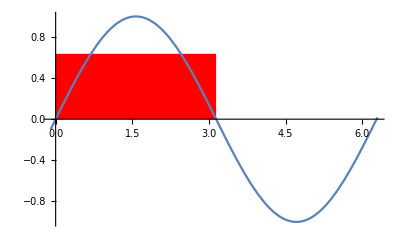

```mathematica
Plot[
Sin[x],
{x,-.1,6.3},
Prolog->{
Red,
Rectangle[{0,0},{Pi,2/Pi}]
}
]
```

```mathematica
Now
```

Tue 9 Nov 2021 14:49:38GMT-5.

```mathematica
xValues = Flatten@Values@NSolve[
D[Sin[x]+Sin[3x]/3+Sin[5x]/5+Sin[7x]/7,x]== 
((Sin[x]+Sin[3x]/3+Sin[5x]/5+Sin[7x]/7/.x->2.8)-(Sin[x]+Sin[3x]/3+Sin[5x]/5+Sin[7x]/7/.x->0.05))/(2.8-0.05)&&
0.05≤x≤2.8
]
```

{0.369041,0.835021,1.11711,1.6392,1.89895,2.40114,2.72214}

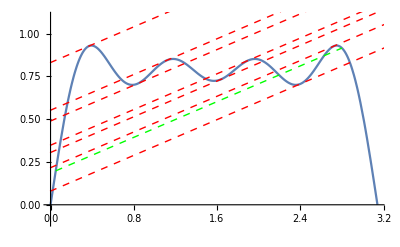

```mathematica
Plot[
Sin[x]+Sin[3x]/3+Sin[5x]/5+Sin[7x]/7,
{x,0,Pi},
PlotRange->{{0,Pi},{-.1,1.1}},
Epilog->{
Green,Thick,Dashed,
Line[
{
{0.05,Sin[x]+Sin[3x]/3+Sin[5x]/5+Sin[7x]/7/.x->0.05},
{2.8, Sin[x]+Sin[3x]/3+Sin[5x]/5+Sin[7x]/7/.x->2.8}
}
],
Red,
Map[
InfiniteLine[
{#,Sin[x]+Sin[3x]/3+Sin[5x]/5+Sin[7x]/7/.x->#},
{1,D[Sin[x]+Sin[3x]/3+Sin[5x]/5+Sin[7x]/7,x]/.x->#}
]&,
xValues
]
}
]
```

```mathematica
Now
```

Mon 22 Nov 2021 13:55:39GMT-5.

```mathematica
Manipulate[
Labeled[
Plot[
{E^(-x/d)Cos[c x],E^(-x/d),-E^(-x/d)},
{x,-1,12},
Filling->Axis
],
NIntegrate[E^(-x/d)Cos[c x],{x,-1,12}]
],
{{c,7},1,10,1},
{{d,2},1,10,1}
]
```